## Plots, Q and J as a function tau for various values of Pmax and Lx

## Initialization

```mathematica
m=1;
```

```mathematica
lxvalues={20,22,24};
pvalues={7,8,9,10,11,12};
```

```mathematica
range[20]={30,40};
range[22]={26,36};
range[24]={26,30};
```

```mathematica
qhtypetonelectrons[{{1,2,0}}]=300;
qhtypetonelectrons[{{2,-2,0}}]=300;
qhtypetonelectrons[{{2,4,0}}]=299;
qhtypetonelectrons[{{3,0,0}}]=300;
qhtypetonelectrons[{{3,0,2}}]=299;
qhtypetonelectrons[{{4,-4,0}}]=298;
qhtypes={{{1,2,0}},{{2,-2,0}},{{2,4,0}},{{3,0,0}},{{3,0,2}},{{4,-4,0}}};
```

```mathematica
qvalues={-1/5,-2/5,-2/5,-3/5,-3/5,-4/5};
jvalues={1/5,2/5,-1/5,3/5,1/5,0};
```

```mathematica
dircharge="C:\\Users\\46730\\Documents\\Data new integration\\Q";
dirspin="C:\\Users\\46730\\Documents\\Data new integration\\J";
filenamenopathcharge1d[lx_, m_, nelectrons_, qhtype_, cutoff_] :=
    	"charge-1d-lx=" <> ToString[Round[lx]] <>
      	"-m=" <> ToString[m] <>
      	"-Ne=" <> ToString[nelectrons] <>
      	"-qhtype=" <> ToString[qhtype[[1, 1]]] <> "_" <> 
      ToString[qhtype[[1, 2]]] <> "_" <> ToString[qhtype[[1, 3]]] <>
      	"-cutoff=" <> ToString[cutoff] <>
      	".wl";
filenamenopathspin1d[lx_, m_, nelectrons_, qhtype_, cutoff_] :=
    	"spin-1d-lx=" <> ToString[Round[lx]] <>
      	"-m=" <> ToString[m] <>
      	"-Ne=" <> ToString[nelectrons] <>
      	"-qhtype=" <> ToString[qhtype[[1, 1]]] <> "_" <> 
      ToString[qhtype[[1, 2]]] <> "_" <> ToString[qhtype[[1, 3]]] <>
      	"-cutoff=" <> ToString[cutoff] <>
      	".wl";
filenamenopathcharge1drev[lx_, m_, nelectrons_, qhtype_, cutoff_] :=
    	"charge-1drev-lx=" <> ToString[Round[lx]] <>
      	"-m=" <> ToString[m] <>
      	"-Ne=" <> ToString[nelectrons] <>
      	"-qhtype=" <> ToString[qhtype[[1, 1]]] <> "_" <> 
      ToString[qhtype[[1, 2]]] <> "_" <> ToString[qhtype[[1, 3]]] <>
      	"-cutoff=" <> ToString[cutoff] <>
      	".wl";
filenamenopathspin1drev[lx_, m_, nelectrons_, qhtype_, cutoff_] :=
    	"spin-1drev-lx=" <> ToString[Round[lx]] <>
      	"-m=" <> ToString[m] <>
      	"-Ne=" <> ToString[nelectrons] <>
      	"-qhtype=" <> ToString[qhtype[[1, 1]]] <> "_" <> 
      ToString[qhtype[[1, 2]]] <> "_" <> ToString[qhtype[[1, 3]]] <>
      	"-cutoff=" <> ToString[cutoff] <>
      	".wl";
```

```mathematica
filenamenopathcharge1dsym[lx_, m_, nelectrons_, qhtype_, cutoff_] :=
    	"charge-1dsym-lx=" <> ToString[Round[lx]] <>
      	"-m=" <> ToString[m] <>
      	"-Ne=" <> ToString[nelectrons] <>
      	"-qhtype=" <> ToString[qhtype[[1, 1]]] <> "_" <> 
      ToString[qhtype[[1, 2]]] <> "_" <> ToString[qhtype[[1, 3]]] <>
      	"-cutoff=" <> ToString[cutoff] <>
      	".wl";
filenamenopathspin1dsym[lx_, m_, nelectrons_, qhtype_, cutoff_] :=
    	"spin-1dsym-lx=" <> ToString[Round[lx]] <>
      	"-m=" <> ToString[m] <>
      	"-Ne=" <> ToString[nelectrons] <>
      	"-qhtype=" <> ToString[qhtype[[1, 1]]] <> "_" <> 
      ToString[qhtype[[1, 2]]] <> "_" <> ToString[qhtype[[1, 3]]] <>
      	"-cutoff=" <> ToString[cutoff] <>
      	".wl";
filenamenopathcharge2d[lx_, m_, nelectrons_, qhtype_, cutoff_] :=
    	"charge-2d-lx=" <> ToString[Round[lx]] <>
      	"-m=" <> ToString[m] <>
      	"-Ne=" <> ToString[nelectrons] <>
      	"-qhtype=" <> ToString[qhtype[[1, 1]]] <> "_" <> 
      ToString[qhtype[[1, 2]]] <> "_" <> ToString[qhtype[[1, 3]]] <>
      	"-cutoff=" <> ToString[cutoff] <>
      	".wl";
filenamenopathspin2d[lx_, m_, nelectrons_, qhtype_, cutoff_] :=
    	"spin-2d-lx=" <> ToString[Round[lx]] <>
      	"-m=" <> ToString[m] <>
      	"-Ne=" <> ToString[nelectrons] <>
      	"-qhtype=" <> ToString[qhtype[[1, 1]]] <> "_" <> 
      ToString[qhtype[[1, 2]]] <> "_" <> ToString[qhtype[[1, 3]]] <>
      	"-cutoff=" <> ToString[cutoff] <>
      	".wl";
filenamenopathcharge2dfull[lx_, m_, nelectrons_, qhtype_, cutoff_] :=
    	"charge-2dfull-lx=" <> ToString[Round[lx]] <>
      	"-m=" <> ToString[m] <>
      	"-Ne=" <> ToString[nelectrons] <>
      	"-qhtype=" <> ToString[qhtype[[1, 1]]] <> "_" <> 
      ToString[qhtype[[1, 2]]] <> "_" <> ToString[qhtype[[1, 3]]] <>
      	"-cutoff=" <> ToString[cutoff] <>
      	".wl";
filenamenopathspin2dfull[lx_, m_, nelectrons_, qhtype_, cutoff_] :=
    	"spin-2dfull-lx=" <> ToString[Round[lx]] <>
      	"-m=" <> ToString[m] <>
      	"-Ne=" <> ToString[nelectrons] <>
      	"-qhtype=" <> ToString[qhtype[[1, 1]]] <> "_" <> 
      ToString[qhtype[[1, 2]]] <> "_" <> ToString[qhtype[[1, 3]]] <>
      	"-cutoff=" <> ToString[cutoff] <>
      	".wl";
```

## Plotting

```mathematica
m=1;
lx=20;
qhtype={{1,2,0}};
pvalues={9,10,11,12};
nelectrons=qhtypetonelectrons[qhtype];
```

```mathematica
datacharge1d=Table[
Import[FileNameJoin[{dircharge,filenamenopathcharge1d[lx,m,nelectrons,qhtype,pv]}]],{pv,pvalues}];
datacharge1drev=Table[
Import[FileNameJoin[{dircharge,filenamenopathcharge1drev[lx,m,nelectrons,qhtype,pv]}]],{pv,pvalues}];
datacharge1dsym=Table[
Import[FileNameJoin[{dircharge,filenamenopathcharge1dsym[lx,m,nelectrons,qhtype,pv]}]],{pv,pvalues}];
datacharge2d=Table[
Import[FileNameJoin[{dircharge,filenamenopathcharge2d[lx,m,nelectrons,qhtype,pv]}]],{pv,pvalues}];
datacharge2dfull=Table[
Import[FileNameJoin[{dircharge,filenamenopathcharge2dfull[lx,m,nelectrons,qhtype,pv]}]],{pv,pvalues}];
```

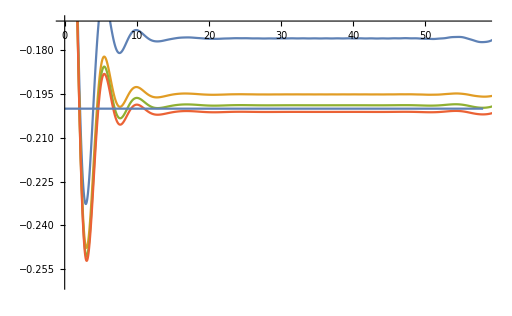

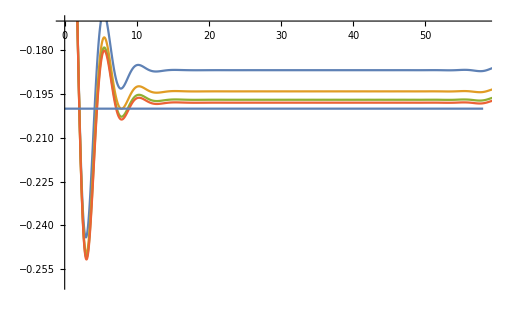

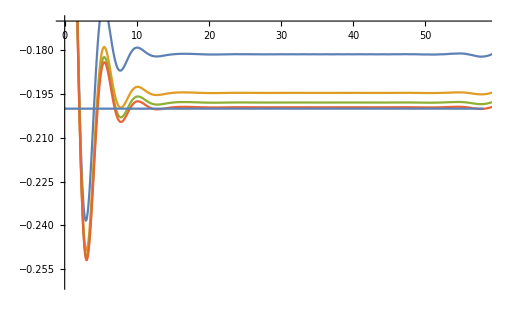

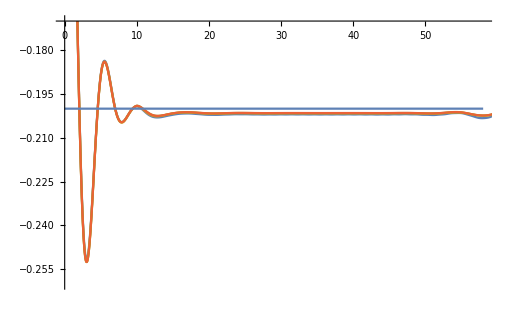

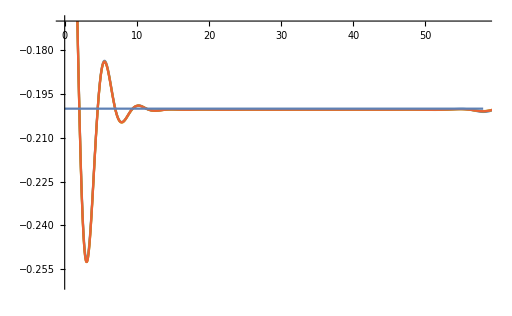

```mathematica
plotchargevstau1d=Show[ListLinePlot[datacharge1d,PlotRange->{{0,58},{-.26,-.17}},ImageSize->512],Plot[-.2,{t,0,58}]]
plotchargevstau1drev=Show[ListLinePlot[datacharge1drev,PlotRange->{{0,58},{-.26,-.17}},ImageSize->512],Plot[-.2,{t,0,58}]]
plotchargevstau1dsym=Show[ListLinePlot[datacharge1dsym,PlotRange->{{0,58},{-.26,-.17}},ImageSize->512],Plot[-.2,{t,0,58}]]
plotchargevstau2d=Show[ListLinePlot[datacharge2d,PlotRange->{{0,58},{-.26,-.17}},ImageSize->512],Plot[-.2,{t,0,58}]]
plotchargevstau2dfull=Show[ListLinePlot[datacharge2dfull,PlotRange->{{0,58},{-.26,-.17}},ImageSize->512],Plot[-.2,{t,0,58}]]
```

```mathematica
dataspin1d=Table[
Import[FileNameJoin[{dirspin,filenamenopathspin1d[lx,m,nelectrons,qhtype,pv]}]],{pv,pvalues}];
dataspin1drev=Table[
Import[FileNameJoin[{dirspin,filenamenopathspin1drev[lx,m,nelectrons,qhtype,pv]}]],{pv,pvalues}];
dataspin1dsym=Table[
Import[FileNameJoin[{dirspin,filenamenopathspin1dsym[lx,m,nelectrons,qhtype,pv]}]],{pv,pvalues}];
dataspin2d=Table[
Import[FileNameJoin[{dirspin,filenamenopathspin2d[lx,m,nelectrons,qhtype,pv]}]],{pv,pvalues}];
dataspin2dfull=Table[
Import[FileNameJoin[{dirspin,filenamenopathspin2dfull[lx,m,nelectrons,qhtype,pv]}]],{pv,pvalues}];
```

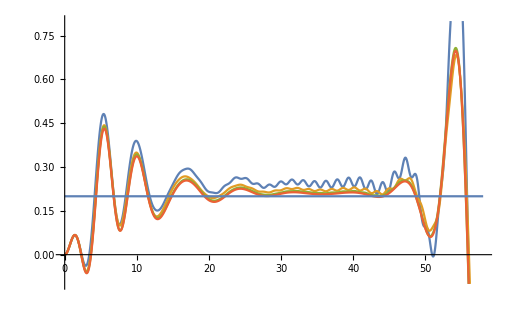

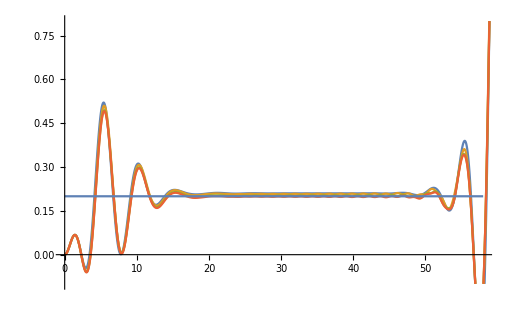

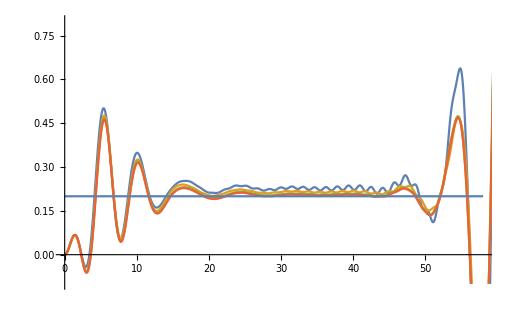

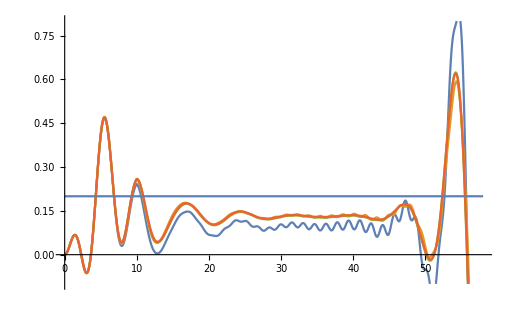

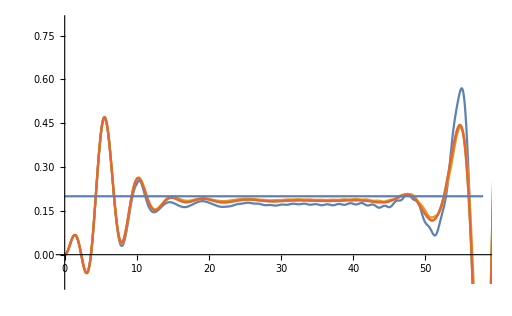

```mathematica
plotspinvstau1d=Show[ListLinePlot[dataspin1d,PlotRange->{{0,58},{-.1,.8}},ImageSize->512],Plot[.2,{t,0,58}]]
plotspinvstau1drev=Show[ListLinePlot[dataspin1drev,PlotRange->{{0,58},{-.1,.8}},ImageSize->512],Plot[.2,{t,0,58}]]
plotspinvstau1dsym=Show[ListLinePlot[dataspin1dsym,PlotRange->{{0,58},{-.1,.8}},ImageSize->512],Plot[.2,{t,0,58}]]
plotspinvstau2d=Show[ListLinePlot[dataspin2d,PlotRange->{{0,58},{-.1,.8}},ImageSize->512],Plot[.2,{t,0,58}]]
plotspinvstau2dfull=Show[ListLinePlot[dataspin2dfull,PlotRange->{{0,58},{-.1,.8}},ImageSize->512],Plot[.2,{t,0,58}]]
```

## Comparing

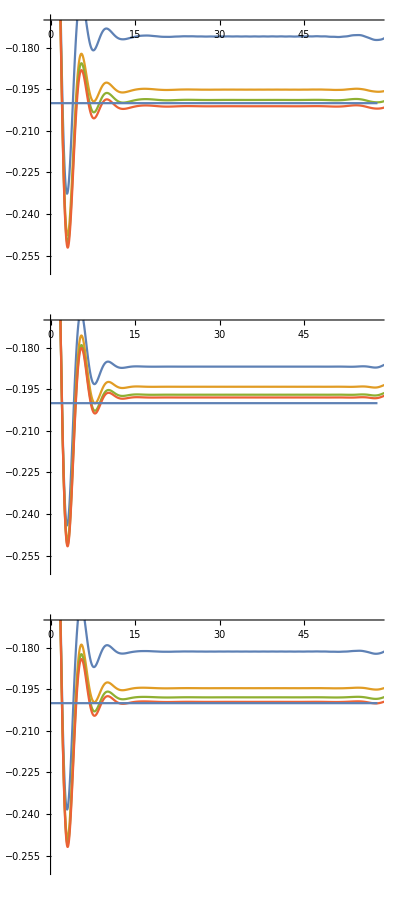
(-Graphics-)

```mathematica
{plotchargevstau1d,plotchargevstau1drev,plotchargevstau1dsym}//MatrixForm
```

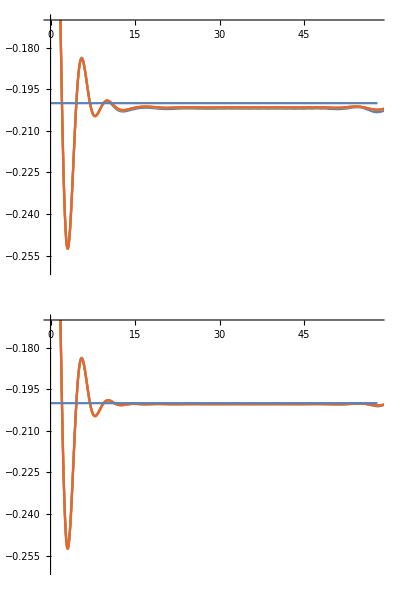
(-Graphics-)

```mathematica
{plotchargevstau2d,plotchargevstau2dfull}//MatrixForm
```

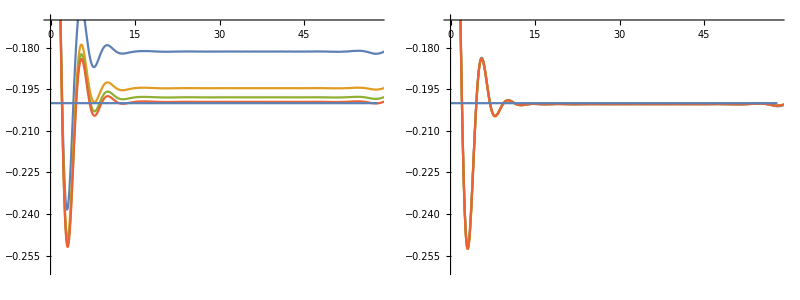
(-Graphics-)

```mathematica
{{plotchargevstau1dsym,plotchargevstau2dfull}}//MatrixForm
```

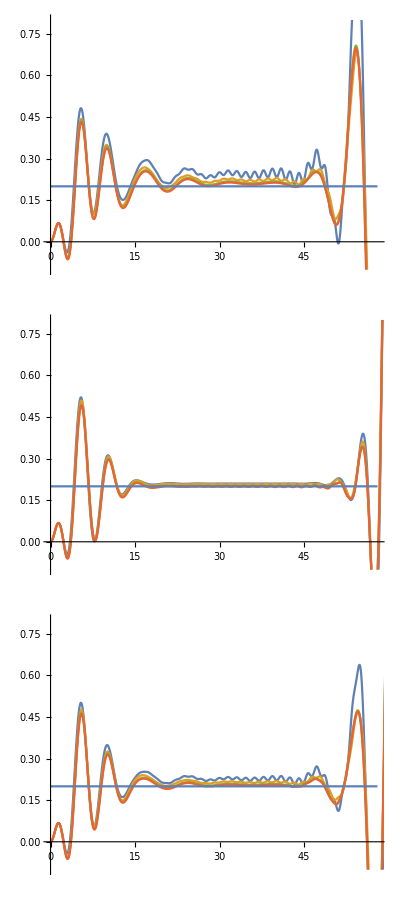
(-Graphics-)

```mathematica
{plotspinvstau1d,plotspinvstau1drev,plotspinvstau1dsym}//MatrixForm
```

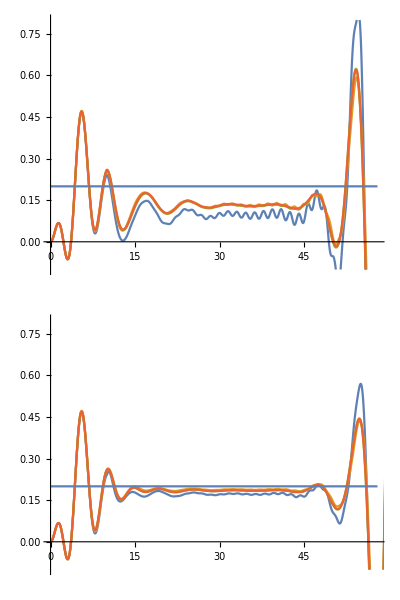
(-Graphics-)

```mathematica
{plotspinvstau2d,plotspinvstau2dfull}//MatrixForm
```

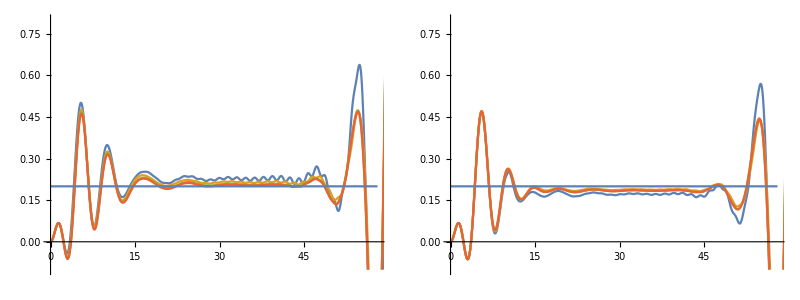
(-Graphics-)

```mathematica
{{plotspinvstau1dsym,plotspinvstau2dfull}}//MatrixForm
```

```mathematica
(*Modified plots here*)
<<MaTeX`
ConfigureMaTeX["Ghostscript"->"C:\\Program Files\\gs\\gs10.03.0\\bin\\gswin64c.exe"];
ConfigureMaTeX["pdfLaTeX"->"C:\\Users\\46730\\MikTeX\\miktex\\bin\\x64\\pdflatex.exe"];
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"];
basesize=16;
SetOptions[{Plot,ListPlot,ArrayPlot,ContourPlot,DiscretePlot3D},BaseStyle->{basesize,Directive[FontFamily->"Times New Roman"]}];
fs=20;
ms=18;
padleft=22;
(*Q vs rmax*)




(*J vs rmax*)
m=1;
lx=20;
pvalues={9,10,11,12};
legright=0.515;

qhtype={{1,2,0}};
nelectrons=qhtypetonelectrons[qhtype];
dataspin1drevσ1=Table[
Import[FileNameJoin[{dirspin,filenamenopathspin1drev[lx,m,nelectrons,qhtype,pv]}]],{pv,pvalues}];
qhtype={{2,-2,0}};
nelectrons=qhtypetonelectrons[qhtype];
dataspin1drevσ2=Table[
Import[FileNameJoin[{dirspin,filenamenopathspin1drev[lx,m,nelectrons,qhtype,pv]}]],{pv,pvalues}];
qhtype={{2,4,0}};
nelectrons=qhtypetonelectrons[qhtype];
dataspin1drevψ1=Table[
Import[FileNameJoin[{dirspin,filenamenopathspin1drev[lx,m,nelectrons,qhtype,pv]}]],{pv,pvalues}];
qhtype={{3,0,0}};
nelectrons=qhtypetonelectrons[qhtype];
dataspin1drev1=Table[
Import[FileNameJoin[{dirspin,filenamenopathspin1drev[lx,m,nelectrons,qhtype,pv]}]],{pv,pvalues}];
qhtype={{3,0,2}};
nelectrons=qhtypetonelectrons[qhtype];
dataspin1drevϵ=Table[
Import[FileNameJoin[{dirspin,filenamenopathspin1drev[lx,m,nelectrons,qhtype,pv]}]],{pv,pvalues}];
qhtype={{4,-4,0}};
nelectrons=qhtypetonelectrons[qhtype];
dataspin1drevψ2=Table[
Import[FileNameJoin[{dirspin,filenamenopathspin1drev[lx,m,nelectrons,qhtype,pv]}]],{pv,pvalues}];

plotspin1drev=Grid[{
{
Show[ListLinePlot[dataspin1drevσ1,PlotRange->{-0.1,0.8},ImageSize->512,AxesLabel->{MaTeX[HoldForm[Subscript[r,max]],FontSize->fs],MaTeX[HoldForm[J],FontSize->fs]},PlotLegends->{Placed[LineLegend[{MaTeX[HoldForm[Subscript[P,max]=9],FontSize->fs],MaTeX[HoldForm[Subscript[P,max]=10],FontSize->fs],MaTeX[HoldForm[Subscript[P,max]=11],FontSize->fs],MaTeX[HoldForm[Subscript[P,max]=12],FontSize->fs]},LegendFunction->(Framed[Style[#]]&),LabelStyle->{FontSize->ms},Spacings->0.06,LegendLayout->"Column",LegendMarkerSize->ms,LegendMargins->2],{legright+0.015,0.65}]},PlotRangeClipping->False,Epilog->Inset[Framed[MaTeX[HoldForm["("Subscript[σ,1] ",1/5)"],FontSize->fs]],{Center,0.8}]],Plot[jvalues[[1]],{x,0,60},PlotStyle->{{Black,Dotted}}],ImagePadding->{{padleft,Automatic},{Automatic,Automatic}},TicksStyle->basesize]
,
Show[ListLinePlot[dataspin1drevσ2,PlotRange->{-0.1,1.1},ImageSize->512,AxesLabel->{MaTeX[HoldForm[Subscript[r,max]],FontSize->fs],MaTeX[HoldForm[J],FontSize->fs]},PlotLegends->{Placed[LineLegend[{MaTeX[HoldForm[Subscript[P,max]=9],FontSize->fs],MaTeX[HoldForm[Subscript[P,max]=10],FontSize->fs],MaTeX[HoldForm[Subscript[P,max]=11],FontSize->fs],MaTeX[HoldForm[Subscript[P,max]=12],FontSize->fs]},LegendFunction->(Framed[Style[#]]&),LabelStyle->{FontSize->ms},Spacings->0.06,LegendLayout->"Column",LegendMarkerSize->ms,LegendMargins->2],{legright+0.02,0.68}]},PlotRangeClipping->False,Epilog->Inset[Framed[MaTeX[HoldForm["("Subscript[σ,2] ",2/5)"],FontSize->fs]],{Center,1.1}]],Plot[jvalues[[2]],{x,0,60},PlotStyle->{{Black,Dotted}}],ImagePadding->{{padleft,Automatic},{Automatic,Automatic}},TicksStyle->basesize]
}
,
{
Show[ListLinePlot[dataspin1drevψ1,PlotRange->{-0.8,1.0},ImageSize->512,AxesLabel->{MaTeX[HoldForm[Subscript[r,max]],FontSize->fs],MaTeX[HoldForm[J],FontSize->fs]},PlotLegends->{Placed[LineLegend[{MaTeX[HoldForm[Subscript[P,max]=9],FontSize->fs],MaTeX[HoldForm[Subscript[P,max]=10],FontSize->fs],MaTeX[HoldForm[Subscript[P,max]=11],FontSize->fs],MaTeX[HoldForm[Subscript[P,max]=12],FontSize->fs]},LegendFunction->(Framed[Style[#]]&),LabelStyle->{FontSize->ms},Spacings->0.06,LegendLayout->"Column",LegendMarkerSize->ms,LegendMargins->2],{legright+0.02,0.69}]},ImageSize->Scaled[1.0],PlotRangeClipping->False,Epilog->Inset[Framed[MaTeX[HoldForm["("Subscript[ψ,1] ",2/5)"],FontSize->fs],Background->Opacity[1,White]],{Center,1.0}]],Plot[jvalues[[3]],{x,0,60},PlotStyle->{{Black,Dotted}}],ImagePadding->{{padleft,Automatic},{Automatic,Automatic}},TicksStyle->basesize]
,
Show[ListLinePlot[dataspin1drev1,PlotRange->{0.0,1.5},ImageSize->512,AxesLabel->{MaTeX[HoldForm[Subscript[r,max]],FontSize->fs],MaTeX[HoldForm[J],FontSize->fs]},PlotLegends->{Placed[LineLegend[{MaTeX[HoldForm[Subscript[P,max]=9],FontSize->fs],MaTeX[HoldForm[Subscript[P,max]=10],FontSize->fs],MaTeX[HoldForm[Subscript[P,max]=11],FontSize->fs],MaTeX[HoldForm[Subscript[P,max]=12],FontSize->fs]},LegendFunction->(Framed[Style[#]]&),LabelStyle->{FontSize->ms},Spacings->0.06,LegendLayout->"Column",LegendMarkerSize->ms,LegendMargins->2],{legright+0.015,0.68}]},ImageSize->Scaled[1.0],PlotRangeClipping->False,Epilog->Inset[Framed[MaTeX[HoldForm["(1,3/5)"],FontSize->fs]],{Center,1.5}]],Plot[jvalues[[4]],{x,0,60},PlotStyle->{{Black,Dotted}}],ImagePadding->{{padleft,Automatic},{Automatic,Automatic}},TicksStyle->basesize]
}
,
{
Show[ListLinePlot[dataspin1drevϵ,PlotRange->{-0.8,1.6},ImageSize->512,AxesLabel->{MaTeX[HoldForm[Subscript[r,max]],FontSize->fs],MaTeX[HoldForm[J],FontSize->fs]},PlotLegends->{Placed[LineLegend[{MaTeX[HoldForm[Subscript[P,max]=9],FontSize->fs],MaTeX[HoldForm[Subscript[P,max]=10],FontSize->fs],MaTeX[HoldForm[Subscript[P,max]=11],FontSize->fs],MaTeX[HoldForm[Subscript[P,max]=12],FontSize->fs]},LegendFunction->(Framed[Style[#]]&),LabelStyle->{FontSize->ms},Spacings->0.06,LegendLayout->"Column",LegendMarkerSize->ms,LegendMargins->2],{legright+0.015,0.70}]},ImageSize->Scaled[1.0],PlotRangeClipping->False,Epilog->Inset[Framed[MaTeX[HoldForm["("ϵ",3/5)"],FontSize->fs]],{Center,1.6}]],Plot[jvalues[[5]],{x,0,60},PlotStyle->{{Black,Dotted}}],ImagePadding->{{padleft,Automatic},{Automatic,Automatic}},TicksStyle->basesize]
,
Show[ListLinePlot[dataspin1drevψ2,PlotRange->{-1.9,1.7},ImageSize->512,AxesLabel->{MaTeX[HoldForm[Subscript[r,max]],FontSize->fs],MaTeX[HoldForm[J],FontSize->fs]},PlotLegends->{Placed[LineLegend[{MaTeX[HoldForm[Subscript[P,max]=9],FontSize->fs],MaTeX[HoldForm[Subscript[P,max]=10],FontSize->fs],MaTeX[HoldForm[Subscript[P,max]=11],FontSize->fs],MaTeX[HoldForm[Subscript[P,max]=12],FontSize->fs]},LegendFunction->(Framed[Style[#]]&),LabelStyle->{FontSize->ms},Spacings->0.06,LegendLayout->"Column",LegendMarkerSize->ms,LegendMargins->2],{legright+0.02,0.23}]},ImageSize->Scaled[1.0],PlotRangeClipping->False,Epilog->Inset[Framed[MaTeX[HoldForm["("Subscript[ψ,2] ",4/5)"],FontSize->fs]],{Center,1.7}]],Plot[jvalues[[6]],{x,0,60},PlotStyle->{{Black,Dotted}}],ImagePadding->{{padleft,Automatic},{Automatic,Automatic}},TicksStyle->basesize]
}
},Frame->All,Spacings->5,Alignment->{Left,Center}]
```

-Graphics-

```mathematica
Export["C:\\Users\\46730\\Documents\\rev J vs rmax, L New.pdf",plotspin1drev]
```

C:\Users\46730\Documents\rev J vs rmax, L New.pdf

```mathematica
Export["jbSigma1List.csv",dataspin1drevσ1[4]]
Export["jbSigma2List.csv",dataspin1drevσ2[4]]
Export["jb1List.csv",dataspin1drev1[4]]
Export["jbPsi1List.csv",dataspin1drevψ1[4]]
Export["jbPsi2List.csv",dataspin1drevψ2[4]]
Export["jbEpsilonList.csv",dataspin1drevϵ[4]]
```

```mathematica
(*Comparison methods*)

qhtype={{1,2,0}};
nelectrons=qhtypetonelectrons[qhtype];
m=1;
lx=20;
pvalues={9,10,11,12};
legright=0.515;

datacharge1drevσ1=Table[
Import[FileNameJoin[{dircharge,filenamenopathcharge1drev[lx,m,nelectrons,qhtype,pv]}]],{pv,pvalues}];
datacharge2dfullσ1=Table[
Import[FileNameJoin[{dircharge,filenamenopathcharge2dfull[lx,m,nelectrons,qhtype,pv]}]],{pv,pvalues}];
dataspin1drevσ1=Table[
Import[FileNameJoin[{dirspin,filenamenopathspin1drev[lx,m,nelectrons,qhtype,pv]}]],{pv,pvalues}];
dataspin2dfullσ1=Table[
Import[FileNameJoin[{dirspin,filenamenopathspin2dfull[lx,m,nelectrons,qhtype,pv]}]],{pv,pvalues}];


plotcompare=Grid[{
{
Show[ListLinePlot[datacharge1drevσ1,PlotRange->{-0.6,0.1},ImageSize->512,AxesLabel->{MaTeX[HoldForm[Subscript[r,max]],FontSize->fs],MaTeX[HoldForm[Q],FontSize->fs]},PlotLegends->{Placed[LineLegend[{MaTeX[HoldForm[Subscript[P,max]=9],FontSize->fs],MaTeX[HoldForm[Subscript[P,max]=10],FontSize->fs],MaTeX[HoldForm[Subscript[P,max]=11],FontSize->fs],MaTeX[HoldForm[Subscript[P,max]=12],FontSize->fs]},LegendFunction->(Framed[Style[#]]&),LabelStyle->{FontSize->ms},Spacings->0.06,LegendLayout->"Column",LegendMarkerSize->ms,LegendMargins->2],{legright+0.01,0.3}]},PlotRangeClipping->False,Epilog->Inset[Framed[MaTeX[HoldForm["Line integral"],FontSize->fs]],{Center,0.1}]],Plot[qvalues[[1]],{x,0,60},PlotStyle->{{Black,Dotted}}],ImagePadding->{{padleft,Automatic},{Automatic,Automatic}},TicksStyle->basesize]
,
Show[ListLinePlot[datacharge2dfullσ1,PlotRange->{-0.6,0.1},ImageSize->512,AxesLabel->{MaTeX[HoldForm[Subscript[r,max]],FontSize->fs],MaTeX[HoldForm[Q],FontSize->fs]},PlotLegends->{Placed[LineLegend[{MaTeX[HoldForm[Subscript[P,max]=9],FontSize->fs],MaTeX[HoldForm[Subscript[P,max]=10],FontSize->fs],MaTeX[HoldForm[Subscript[P,max]=11],FontSize->fs],MaTeX[HoldForm[Subscript[P,max]=12],FontSize->fs]},LegendFunction->(Framed[Style[#]]&),LabelStyle->{FontSize->ms},Spacings->0.06,LegendLayout->"Column",LegendMarkerSize->ms,LegendMargins->2],{legright+0.01,0.3}]},PlotRangeClipping->False,Epilog->Inset[Framed[MaTeX[HoldForm["Double integral"],FontSize->fs]],{Center,0.1}]],Plot[qvalues[[1]],{x,0,60},PlotStyle->{{Black,Dotted}}],ImagePadding->{{padleft,Automatic},{Automatic,Automatic}},TicksStyle->basesize]
}
,
{
Show[ListLinePlot[dataspin1drevσ1,PlotRange->{-0.4,1.0},ImageSize->512,AxesLabel->{MaTeX[HoldForm[Subscript[r,max]],FontSize->fs],MaTeX[HoldForm[J],FontSize->fs]},PlotLegends->{Placed[LineLegend[{MaTeX[HoldForm[Subscript[P,max]=9],FontSize->fs],MaTeX[HoldForm[Subscript[P,max]=10],FontSize->fs],MaTeX[HoldForm[Subscript[P,max]=11],FontSize->fs],MaTeX[HoldForm[Subscript[P,max]=12],FontSize->fs]},LegendFunction->(Framed[Style[#]]&),LabelStyle->{FontSize->ms},Spacings->0.06,LegendLayout->"Column",LegendMarkerSize->ms,LegendMargins->2],{legright+0.012,0.68}]},ImageSize->Scaled[1.0],PlotRangeClipping->False,Epilog->Inset[Framed[MaTeX[HoldForm["Line integral"],FontSize->fs],Background->Opacity[1,White]],{Center,1.0}]],Plot[jvalues[[1]],{x,0,60},PlotStyle->{{Black,Dotted}}],ImagePadding->{{padleft,Automatic},{Automatic,Automatic}},TicksStyle->basesize]
,
Show[ListLinePlot[dataspin2dfullσ1,PlotRange->{-0.4,1.0},ImageSize->512,AxesLabel->{MaTeX[HoldForm[Subscript[r,max]],FontSize->fs],MaTeX[HoldForm[J],FontSize->fs]},PlotLegends->{Placed[LineLegend[{MaTeX[HoldForm[Subscript[P,max]=9],FontSize->fs],MaTeX[HoldForm[Subscript[P,max]=10],FontSize->fs],MaTeX[HoldForm[Subscript[P,max]=11],FontSize->fs],MaTeX[HoldForm[Subscript[P,max]=12],FontSize->fs]},LegendFunction->(Framed[Style[#]]&),LabelStyle->{FontSize->ms},Spacings->0.06,LegendLayout->"Column",LegendMarkerSize->ms,LegendMargins->2],{legright+0.012,0.68}]},ImageSize->Scaled[1.0],PlotRangeClipping->False,Epilog->Inset[Framed[MaTeX[HoldForm["Double integral"],FontSize->fs]],{Center,1.0}]],Plot[jvalues[[1]],{x,0,60},PlotStyle->{{Black,Dotted}}],ImagePadding->{{padleft,Automatic},{Automatic,Automatic}},TicksStyle->basesize]
}
},Frame->All,Spacings->5,Alignment->{Left,Center}]
```

-Graphics-

```mathematica
Export["C:\\Users\\46730\\Documents\\comparison integrations 1d rev 2d full New.pdf",plotcompare]
```

C:\Users\46730\Documents\comparison integrations 1d rev 2d full New.pdf

```mathematica
"C:\\Users\\46730\\Documents\\rev J vs rmax, L.pdf"
```

C:\Users\46730\Documents\rev J vs rmax, L.pdf

```mathematica
(*Charges all QHs*)

m=1;
lx=20;
pvalues={12};
legright=0.515;
```

```mathematica
qhtype={{1,2,0}};
nelectrons=qhtypetonelectrons[qhtype];
datacharge2dfullσ1=Table[
Import[FileNameJoin[{dircharge,filenamenopathcharge2dfull[lx,m,nelectrons,qhtype,pv]}]],{pv,pvalues}];
qhtype={{2,-2,0}};
nelectrons=qhtypetonelectrons[qhtype];
datacharge2dfullσ2=Table[
Import[FileNameJoin[{dircharge,filenamenopathcharge2dfull[lx,m,nelectrons,qhtype,pv]}]],{pv,pvalues}];
qhtype={{2,4,0}};
nelectrons=qhtypetonelectrons[qhtype];
datacharge2dfullψ1=Table[
Import[FileNameJoin[{dircharge,filenamenopathcharge2dfull[lx,m,nelectrons,qhtype,pv]}]],{pv,pvalues}];
qhtype={{3,0,0}};
nelectrons=qhtypetonelectrons[qhtype];
datacharge2dfull1=Table[
Import[FileNameJoin[{dircharge,filenamenopathcharge2dfull[lx,m,nelectrons,qhtype,pv]}]],{pv,pvalues}];
qhtype={{3,0,2}};
nelectrons=qhtypetonelectrons[qhtype];
datacharge2dfullϵ=Table[
Import[FileNameJoin[{dircharge,filenamenopathcharge2dfull[lx,m,nelectrons,qhtype,pv]}]],{pv,pvalues}];
qhtype={{4,-4,0}};
nelectrons=qhtypetonelectrons[qhtype];
datacharge2dfullψ2=Table[
Import[FileNameJoin[{dircharge,filenamenopathcharge2dfull[lx,m,nelectrons,qhtype,pv]}]],{pv,pvalues}];
```

```mathematica
endpt=2000;
plotcharge2dfullall=ListLinePlot[{datacharge2dfullσ1[[1]][[1;;endpt]],datacharge2dfullσ2[[1]][[1;;endpt]],datacharge2dfullψ1[[1]][[1;;endpt]],datacharge2dfull1[[1]][[1;;endpt]],datacharge2dfullϵ[[1]][[1;;endpt]],datacharge2dfullψ2[[1]][[1;;endpt]]},PlotRange->{-1.0,0.1},ImageSize->512,AxesLabel->{MaTeX[HoldForm[Subscript[r,max]],FontSize->fs],MaTeX[HoldForm[Q],FontSize->fs]},PlotRangeClipping->False,TicksStyle->basesize,PlotLegends->{Placed[LineLegend[{MaTeX[HoldForm["("Subscript[σ,1]",1/5)"],FontSize->fs],MaTeX[HoldForm["("Subscript[σ,2]",2/5)"],FontSize->fs],MaTeX[HoldForm["("Subscript[ψ,1]",2/5)"],FontSize->fs],MaTeX[HoldForm["(1,3/5)"],FontSize->fs],MaTeX[HoldForm["("ϵ",3/5)"],FontSize->fs],MaTeX[HoldForm["("Subscript[ψ,2]",4/5)"],FontSize->fs]},LegendFunction->(Framed[Style[#]]&),LabelStyle->{FontSize->ms},Spacings->0.12,LegendLayout->"Column",LegendMarkerSize->ms,LegendMargins->5],{1.01,0.5}]}];
lineplots=Plot[{qvalues[[1]],qvalues[[2]],qvalues[[3]],qvalues[[4]],qvalues[[5]],qvalues[[6]]},{x,0,endpt/100},PlotStyle->{{Black,Dotted}}];
chargesplot=Show[plotcharge2dfullall,lineplots]
```

-Graphics-

```mathematica
Export["C:\\Users\\46730\\Documents\\charges 2d full New.pdf",chargesplot]
```

C:\Users\46730\Documents\charges 2d full New.pdf